## Linear Background Profile

```mathematica
sys=I D[{psi1[x],psi2[x]},x]==Asys {{0,Exp[I (a (x+bn/a)^2/2-bn^2/(2 a) + n phi)]},{Exp[-I( a (x+bn/a)^2/2-bn^2/(2 a)+ n phi)],0}}.{psi1[x],psi2[x]}
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={Asys ⅇ^(ⅈ (-bn^2/(2 a)+n phi+1/2 a (bn/a+x)^2)) psi2[x],Asys ⅇ^(-ⅈ (-bn^2/(2 a)+n phi+1/2 a (bn/a+x)^2)) psi1[x]}

```mathematica
sol=DSolve[sys&&{psi1[0],psi2[0]}=={1,0},{psi1,psi2},x];
psi2/.First@sol//FullSimplify
```

Function[{x},((-1)^(1/4) √2 Asys ⅇ^((ⅈ bn^2)/(2 a)-ⅈ n phi-1/2 ⅈ a (bn/a+x)^2) (-bn HermiteH[-1-(ⅈ Asys^2)/a,((-1)^(1/4) bn)/(√2 √a)+((-1)^(1/4) √a x)/(√2)] Hypergeometric1F1[1+(ⅈ Asys^2)/(2 a),3/2,(ⅈ bn^2)/(2 a)]+bn HermiteH[-1-(ⅈ Asys^2)/a,((-1)^(1/4) bn)/(√2 √a)] Hypergeometric1F1[1+(ⅈ Asys^2)/(2 a),3/2,(((-1)^(1/4) bn)/(√2 √a)+((-1)^(1/4) √a x)/(√2))^2]+a x HermiteH[-1-(ⅈ Asys^2)/a,((-1)^(1/4) bn)/(√2 √a)] Hypergeometric1F1[1+(ⅈ Asys^2)/(2 a),3/2,(((-1)^(1/4) bn)/(√2 √a)+((-1)^(1/4) √a x)/(√2))^2]))/(√a ((-1)^(3/4) √2 √a HermiteH[-1-(ⅈ Asys^2)/a,((-1)^(1/4) bn)/(√2 √a)] Hypergeometric1F1[(ⅈ Asys^2)/(2 a),1/2,(ⅈ bn^2)/(2 a)]-bn HermiteH[-(ⅈ Asys^2)/a,((-1)^(1/4) bn)/(√2 √a)] Hypergeometric1F1[1+(ⅈ Asys^2)/(2 a),3/2,(ⅈ bn^2)/(2 a)]))]

```mathematica
sys2=I D[{psi1[x],psi2[x]},x]==Asys {{0,Exp[I (amp (x-extrabeta)^2-extrapha)]},{Exp[-I(amp (x-extrabeta)^2-extrapha)],0}}.{psi1[x],psi2[x]}
sol2=DSolve[sys2&&{psi1[0],psi2[0]}=={1,0},{psi1,psi2},x];
psi1/.First@sol2
psi2/.First@sol2
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={Asys ⅇ^(ⅈ (-extrapha+amp (-extrabeta+x)^2)) psi2[x],Asys ⅇ^(-ⅈ (-extrapha+amp (-extrabeta+x)^2)) psi1[x]}

Function[{x},((-1)^(3/4) HermiteH[-1-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[(ⅈ Asys^2)/(4 amp),1/2,(-(-1)^(1/4) √amp extrabeta+(-1)^(1/4) √amp x)^2]+√amp extrabeta HermiteH[-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta+(-1)^(1/4) √amp x] Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,ⅈ amp extrabeta^2])/((-1)^(3/4) HermiteH[-1-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[(ⅈ Asys^2)/(4 amp),1/2,ⅈ amp extrabeta^2]+√amp extrabeta HermiteH[-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,ⅈ amp extrabeta^2])]

Function[{x},-(((-1)^(1/4) Asys ⅇ^(ⅈ extrapha-ⅈ amp (-extrabeta+x)^2) (-extrabeta HermiteH[-1-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta+(-1)^(1/4) √amp x] Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,ⅈ amp extrabeta^2]+extrabeta HermiteH[-1-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,(-(-1)^(1/4) √amp extrabeta+(-1)^(1/4) √amp x)^2]-x HermiteH[-1-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,(-(-1)^(1/4) √amp extrabeta+(-1)^(1/4) √amp x)^2]))/((-1)^(3/4) HermiteH[-1-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[(ⅈ Asys^2)/(4 amp),1/2,ⅈ amp extrabeta^2]+√amp extrabeta HermiteH[-(ⅈ Asys^2)/(2 amp),-(-1)^(1/4) √amp extrabeta] Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,ⅈ amp extrabeta^2]))]

```mathematica
sys3=I D[{psi1[x],psi2[x]},x]==Asys {{0,Exp[I (amp x^2)]},{Exp[-I(amp x^2)],0}}.{psi1[x],psi2[x]}
sol3=DSolve[sys3&&{psi1[0],psi2[0]}=={1,0},{psi1,psi2},x];
psi2/.First@sol3
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={Asys ⅇ^(ⅈ amp x^2) psi2[x],Asys ⅇ^(-ⅈ amp x^2) psi1[x]}

Function[{x},-ⅈ Asys ⅇ^(-ⅈ amp x^2) x Hypergeometric1F1[1+(ⅈ Asys^2)/(4 amp),3/2,ⅈ amp x^2]]

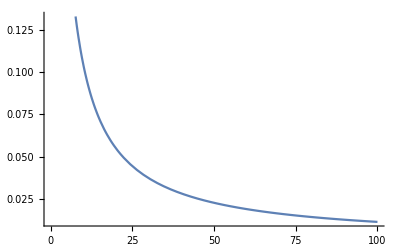

```mathematica
Plot[Re@HermiteH[-1,(0.5+0.3x)(-1)^(1/4)],{x,0,100}]
```

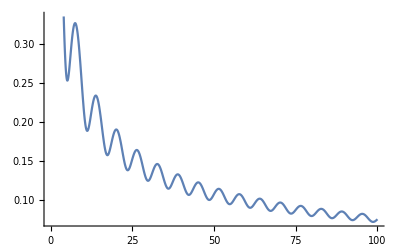

```mathematica
Plot[Abs@Hypergeometric1F1[1+0.1I,3/2,I x],{x,0,100}]
```